```mathematica
ClearAll["Global`*"]
```

```mathematica
folder=FileNameJoin[{"Desktop","TESI MAGISTRALE","Parte scritta","Immagini Tesi"}];
```

# Preheating scenario

```mathematica
(* adimensional time *)
zIn=2/3;          
zMax=25;         

(* q parameter: Broad resonance *)
q=10^4;
Print["\n coupling value g = ",g = Sqrt[(q*4*(6*10^-6)^2)/2.32^2]]
```

coupling value g = 0.000517241

## Solving Background dynamic

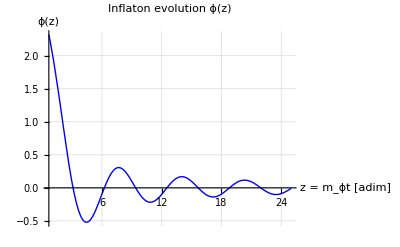

```mathematica
(* Hubble factor: matter era *)
H[z_]:=2/(3z);

(* Solution Inflaton *) 
eqϕ=ϕ''[z]+3*H[z]*ϕ'[z]+ϕ[z]==0;
ϕIn=2.32;                         (* in units of reduced Planck mass *)
dϕIn=-0.78;                    (* in units of reduced Planck mass *)
bcϕ={ϕ[zIn]==ϕIn,ϕ'[zIn]==dϕIn};
solϕ=DSolveValue[{eqϕ,bcϕ},ϕ,z]//FullSimplify;

(* Plots *)
ϕplot = Plot[solϕ[z],{z,zIn,zMax},PlotRange->All,AxesLabel->{"z = m_ϕt [adim]","ϕ(z)"},PlotLabel->"Inflaton evolution ϕ(z)",PlotStyle->{Blue,Thick},GridLines->Automatic]
```

## Fit

{a→2.37322,b→1.52762}

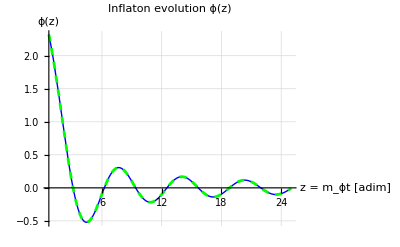

```mathematica
solϕnumerical=NDSolveValue[{eqϕ,bcϕ},ϕ,{z,zIn,zMax}];
dataInflaton=Table[{zVal,solϕnumerical[zVal]},{zVal,zIn,zMax,0.1}];

fitParams=FindFit[dataInflaton,(a/z)*Cos[z-b],{a,b},z]

fitplot = Plot[(a/z)*Cos[z-b]/.fitParams,{z,zIn,zMax},PlotStyle->{Dashed,Green},PlotRange->All];
Show[{ϕplot,fitplot}]
```

## Resonance parameter

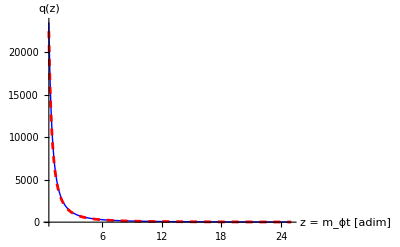

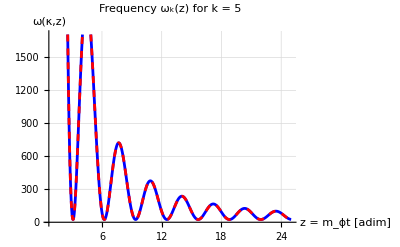

```mathematica
(* q effective in expanding universe *)
qeff[z_]:=q*((a/(z+b))/ϕIn)^2 /. fitParams;

bpar = b/.fitParams[[2]];
(* Plot q effective *)
qPlot = Plot[{qeff[z-bpar],q*(z^-2)},{z,zIn,zMax},PlotRange->All,AxesLabel->{"z = m_ϕt [adim]","q(z)"},PlotStyle->{{Thick,Blue},{Dashed,Red}}]

Apar[z_,k_]:=k^2 + 2qeff[z];
ωMathieu[z_,k_]:=Apar[z,k]+ 2qeff[z]Cos[2z];

ω2[z_,k_]:=k^2+4*q*(solϕ[z]/ϕIn)^2;

(* Plot equivalence *)
ωPlot1 = Plot[ωMathieu[z-bpar,5],{z,zIn,zMax},PlotStyle->{Dashed,Red}];
ω2Plot = Plot[ω2[z,5],{z,zIn,zMax},PlotStyle->{Blue},AxesLabel->{"z = m_ϕt [adim]","ω(κ,z)"},PlotLabel->Style[StringForm["Frequency ω_k(z) for k = ``",5]],PlotStyle->{Blue,Thick},GridLines->Automatic];
Show[{ω2Plot,ωPlot1}]
```

## Stability / Instability chart and Time evolution

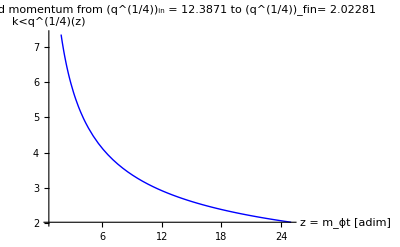

```mathematica
Plot[qeff[z-bpar]^(1/4),{z,zIn,zMax},AxesLabel->{"z = m_ϕt [adim]","k<q^(1/4)(z)"},PlotLabel->Style[StringForm["Excited momentum from (q^(1/4))_in = `` to (q^(1/4))_fin= ``",qeff[zIn-bpar]^(1/4),qeff[zMax-bpar]^(1/4)]],PlotStyle->{Thick,Blue}]
```

```mathematica
(*
z1=10;          (* initial time *)
z2=15;         (* intermediate time *)
z3=18;         (* final time *)

q1=qeff[z1];
q2=qeff[z2];
q3=qeff[z3];

qMaxPlot=q1+10;
AMaxPlot = 200;

mathieuBands=RegionPlot[Or@@Table[MathieuCharacteristicB[n,qval]<Aval<MathieuCharacteristicA[n,qval],{n,1,15}],{qval,0.01,qMaxPlot},{Aval,0,AMaxPlot},PlotPoints->100,BoundaryStyle->Thin,PlotStyle->Directive[Opacity[0.2],Red],Frame->True,FrameLabel->{"q","A"}];

traiettoriaModo[k_,qval_]:=k^2+2*qval;

plotTrajectory=Plot[{traiettoriaModo[1,qv],traiettoriaModo[5,qv],traiettoriaModo[8,qv]},{qv,0,qMaxPlot},PlotStyle->{{Blue,Thick},{Darker[Green],Thick},{Orange,Thick}},PlotLegends->{"κ = 1","κ = 5","κ = 8"}];

pointZ1=Graphics[{PointSize[0.018],Blue,Point[{q1,traiettoriaModo[1,q1]}],PointSize[0.018],Darker[Green],Point[{q1,traiettoriaModo[5,q1]}],PointSize[0.018],Orange,Point[{q1,traiettoriaModo[8,q1]}],Text[Style[StringForm["z = ``",z1],Bold,10,Black,Background->White],{q1+3,traiettoriaModo[1,q1]-6}]}];

pointZ2=Graphics[{PointSize[0.018],Blue,Point[{q2,traiettoriaModo[1,q2]}],PointSize[0.018],Darker[Green],Point[{q2,traiettoriaModo[5,q2]}],PointSize[0.018],Orange,Point[{q2,traiettoriaModo[8,q2]}],Text[Style[StringForm["z = ``",z2],Bold,10,Black,Background->White],{q2+3,traiettoriaModo[8,q2]+6}]}];

pointZ3=Graphics[{PointSize[0.018],Blue,Point[{q3,traiettoriaModo[1,q3]}],PointSize[0.018],Darker[Green],Point[{q3,traiettoriaModo[5,q3]}],PointSize[0.018],Orange,Point[{q3,traiettoriaModo[8,q3]}],Text[Style[StringForm["z = ``",z3],Bold,10,Black,Background->White],{q3+4,traiettoriaModo[8,q3]-6}]}];

ChartMathieu=Show[{mathieuBands,plotTrajectory,pointZ1,pointZ2,pointZ3},PlotRange->{{0,qMaxPlot},{0,AMaxPlot}},GridLines->Automatic]

Export[FileNameJoin[{folder,"chart_Mathieu_preheating.pdf"}],ChartMathieu];
*)
```

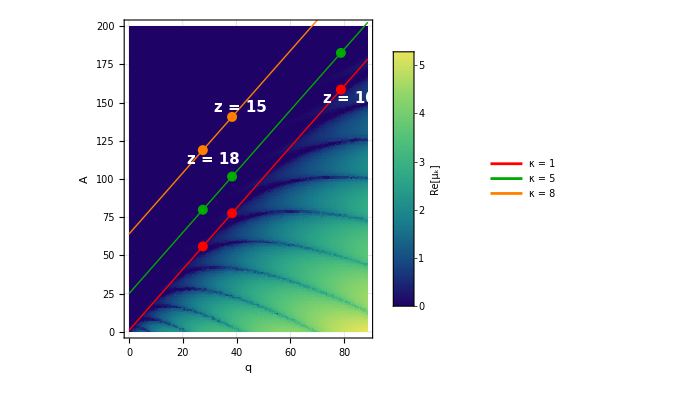

```mathematica
μ[A_?NumericQ,q_?NumericQ]:=Abs[Im[MathieuCharacteristicExponent[A,q]]];

z1=10;          (* initial time *)
z2=15;         (* intermediate time *)
z3=18;         (* final time *)

q1=qeff[z1];
q2=qeff[z2];
q3=qeff[z3];

qMaxPlot=q1+10;
AMaxPlot = 200;

traiettoriaModo[k_,qval_]:=k^2+2*qval;

plotFloquet=DensityPlot[μ[Aval,qval],{qval,0.01,qMaxPlot},{Aval,0,AMaxPlot},PlotPoints->100(*500*),MaxRecursion->2(*5*),ColorFunction->"BlueGreenYellow",PlotRange->All,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],PlotLegends->BarLegend[Automatic,LegendLabel->Style["Re[μ_k]",Bold,12,FontFamily->"Times"],LegendMarkerSize->180],Frame->True,FrameLabel->{Style[Row[{Style["q","Times"]}],20,"Times"],Style[Row[{Style["A","Times"]}],20,"Times"]}];

plotTrajectory2=Plot[{traiettoriaModo[1,qv],traiettoriaModo[5,qv],traiettoriaModo[8,qv]},{qv,0,qMaxPlot},PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Orange,Thick}},PlotLegends->{"κ = 1","κ = 5","κ = 8"}];

pointZ1=Graphics[{PointSize[0.018],Red,Point[{q1,traiettoriaModo[1,q1]}],PointSize[0.018],Darker[Green],Point[{q1,traiettoriaModo[5,q1]}],PointSize[0.018],Orange,Point[{q1,traiettoriaModo[8,q1]}],Text[Style[StringForm["z = ``",z1],Bold,15,White],{q1+3,traiettoriaModo[1,q1]-6}]}];

pointZ2=Graphics[{PointSize[0.018],Red,Point[{q2,traiettoriaModo[1,q2]}],PointSize[0.018],Darker[Green],Point[{q2,traiettoriaModo[5,q2]}],PointSize[0.018],Orange,Point[{q2,traiettoriaModo[8,q2]}],Text[Style[StringForm["z = ``",z2],Bold,15,White],{q2+3,traiettoriaModo[8,q2]+6}]}];

pointZ3=Graphics[{PointSize[0.018],Red,Point[{q3,traiettoriaModo[1,q3]}],PointSize[0.018],Darker[Green],Point[{q3,traiettoriaModo[5,q3]}],PointSize[0.018],Orange,Point[{q3,traiettoriaModo[8,q3]}],Text[Style[StringForm["z = ``",z3],Bold,15,White],{q3+4,traiettoriaModo[8,q3]-6}]}];

ChartMathieu2=Show[{plotFloquet,plotTrajectory2,pointZ1,pointZ2,pointZ3},PlotRange->{{0,qMaxPlot},{0,AMaxPlot}},GridLines->Automatic]
(*
Export[FileNameJoin[{folder,"chart_Mathieu2_preheating.png"}],ChartMathieu2,ImageResolution->300];
*)
```

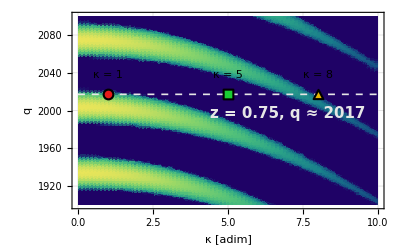

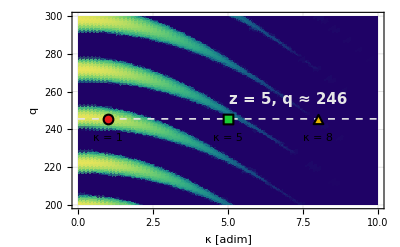

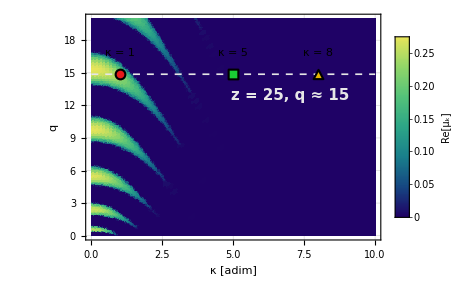

```mathematica
μcoeff[k_?NumericQ,qval_?NumericQ]:=Abs[Im[MathieuCharacteristicExponent[k^2+2*qval,qval]]];

createMathieuChart[zSlice_,qMin_,qMax_,showLegend_Symbol]:=Module[{qSlice,kMax,plotFloquetkq,sliceLine,markerSize,markerCircle,markerSquare,markerTriangle,pointsGroup,labelStyle,yOffset,labels,legendOption,aspect},

qSlice = qeff[zSlice];
kMax=10; (* qSlice^(1/4)+10*)

yOffset=0.1*(qMax-qMin);

aspect=If[showLegend,1/GoldenRatio*1.15,1/GoldenRatio];
legendOption=If[showLegend,PlotLegends->BarLegend[Automatic,LegendLabel->Style["Re[μ_k]",Bold,15,FontFamily->"Times"],LegendMarkerSize->180],PlotLegends->None];

plotFloquetkq=DensityPlot[μcoeff[k,qval],{k,0,kMax},{qval,qMin,qMax},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,Evaluate[legendOption],Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["κ [adim]","Times"]}],20,"Times"],Style[Row[{Style["q","Times"]}],20,"Times"]},FrameTicksStyle->Directive[FontSize->11,FontFamily->"Times"],GridLines->Automatic,GridLinesStyle->Directive[Opacity[0.15],White],Method->{"DefaultBoundaryStyle"->None}];

sliceLine=Graphics[{Thickness[0.003],Dashed,GrayLevel[0.9],Line[{{0,qSlice},{kMax,qSlice}}]}];

markerSize=Offset[10];
markerCircle=Inset[Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],RGBColor[0.9,0.1,0.1],Disk[]}],{1,qSlice},Center,markerSize];
markerSquare=Inset[Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],RGBColor[0.1,0.8,0.2],Rectangle[{-1,-1},{1,1}]}],{5,qSlice},Center,markerSize];
markerTriangle=Inset[Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],RGBColor[0.9,0.7,0.0],Polygon[{{0,1.1},{-1,-0.8},{1,-0.8}}]}],{8,qSlice},Center,markerSize];
pointsGroup=Graphics[{markerCircle,markerSquare,markerTriangle}];

labelStyle[txt_]:=Style[txt,FontFamily->"Times",Italic,15,Black];
labels=Graphics[{Text[Framed[labelStyle["κ = 1"],FrameStyle->GrayLevel[0.8],Background->White,FrameMargins->2,RoundingRadius->2],{1,qSlice+yOffset}],Text[Framed[labelStyle["κ = 5"],FrameStyle->GrayLevel[0.8],Background->White,FrameMargins->2,RoundingRadius->2],{5,qSlice+yOffset}],Text[Framed[labelStyle["κ = 8"],FrameStyle->GrayLevel[0.8],Background->White,FrameMargins->2,RoundingRadius->2],{8,qSlice+yOffset}],Text[Style[Row[{"z = ",zSlice,", q ≈ ",Round[qSlice]}],FontFamily->"Times",Bold,15,GrayLevel[0.9]],{kMax-3,qSlice-yOffset}]}];

Show[plotFloquetkq,sliceLine,pointsGroup,labels,PlotRange->{{0,kMax},{qMin,qMax}},AspectRatio->aspect]
];

chart2000=createMathieuChart[0.75,1900,2100,False]
(*
Export[FileNameJoin[{folder,"chart_Mathieu_kq_2000.png"}],chart2000,ImageResolution->300];
*)
chart100=createMathieuChart[5,300,200,False]
(*
Export[FileNameJoin[{folder,"chart_Mathieu_kq_100.png"}],chart100,ImageResolution->300];
*)
chart10=createMathieuChart[25,0,20,True]
(*
Export[FileNameJoin[{folder,"chart_Mathieu_kq_10.png"}],chart10,ImageResolution->300];
*)
```

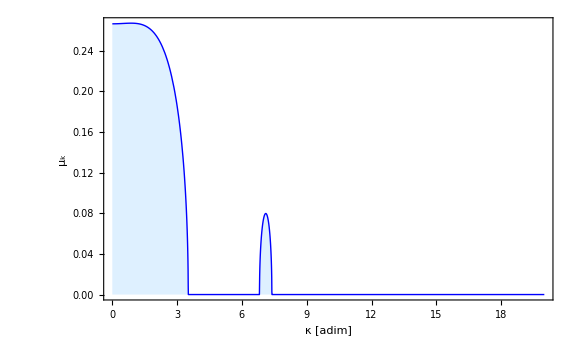

```mathematica
tassoCrescita[k_,qVal_]:=Module[{AVal,nu},
AVal = k^2 + 2qVal;
nu=MathieuCharacteristicExponent[AVal,qVal];
If[Element[nu,Reals],0.0,Abs[Im[nu]]]]

Plot[tassoCrescita[k,qeff[2]],{k,0,20},PlotRange->All,Frame->True,FrameLabel->{"κ [adim]","μ_k"},PlotStyle->{Directive[Blue,Thick]},Filling->{1->{Axis,LightBlue}},ImageSize->Large]
```

## Daughter dynamic

```mathematica
(* Solution Spectator *) 
eqχ=χ''[z]+ω2[z,k]*χ[z]==0;
bcχ={χ[zIn]==1/(√(2Sqrt[ω2[zIn,k]])),χ'[zIn]==-I √(Sqrt[ω2[zIn,k]]/2)};
solχ=ParametricNDSolveValue[{eqχ,bcχ[[1]],bcχ[[2]]},χ,{z,zIn,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];
χsol[k_,z_]:=solχ[k][z];

(* Number density spectator *)
numberχ[k_,z_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[z]]^2/(2*Sqrt[ω2[z,k]])+Sqrt[ω2[z,k]]/2 Abs[χsolK[z]]^2-1/2
];
```

## Plots

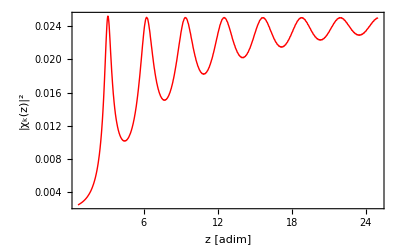

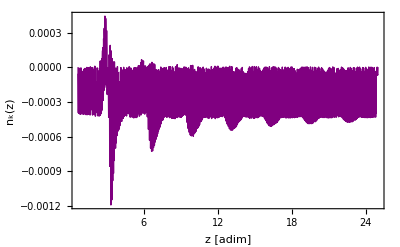

```mathematica
plotχ2 =Plot[Abs[χsol[20,z]]^2,{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{Red,Thick}]
plotnχ2 =Plot[numberχ[20,z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["n_k(z)","Times"]}],15,"Times"]},PlotStyle->{Purple,Thick}]
(*
Export[FileNameJoin[{folder,"plot_chi_k2_preheating.pdf"}],plotχ2];
Export[FileNameJoin[{folder,"plot_nchi_k2_preheating.pdf"}],plotnχ2];
*)
```

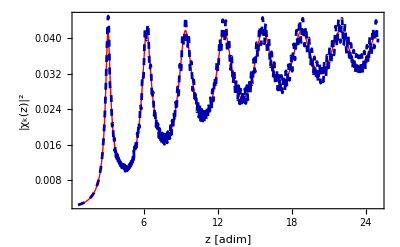

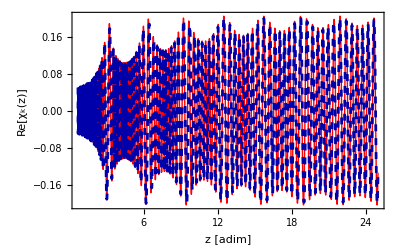

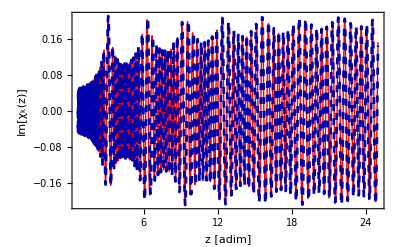

```mathematica
(* κ>12 Equivalent to vacuum evolution *)

(*fase del vuoto dinamico θ'[z]*)
eqθ=θ'[z]==Sqrt[ω2[z,k]];
bcθ=θ[zIn]==0;
solθ=ParametricNDSolveValue[{eqθ,bcθ},θ,{z,zIn,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];
θsol[k_,z_]:=solθ[k][z];

(*Vacuum mode function*)
χvac[k_,z_]:=Exp[-I*θsol[k,z]]/Sqrt[2*Sqrt[ω2[z,k]]];

plotdiffχvacuum =Plot[{Abs[χvac[12,z]]^2,Abs[χsol[12,z]]^2},{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{{Red,Thick},{Dashed,Darker[Blue]}}]

plotReχvacuum =Plot[{Re[χvac[12,z]],Re[χsol[12,z]]},{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["Re[χ_k(z)]","Times"]}],15,"Times"]},PlotStyle->{{Red,Thick},{Dashed,Darker[Blue]}}]

plotImχvacuum =Plot[{Im[χvac[12,z]],Im[χsol[12,z]]},{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["Im[χ_k(z)]","Times"]}],15,"Times"]},PlotStyle->{{Red,Thick},{Dashed,Darker[Blue]}}]
```

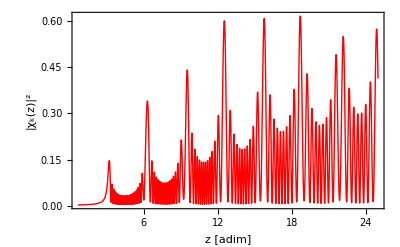

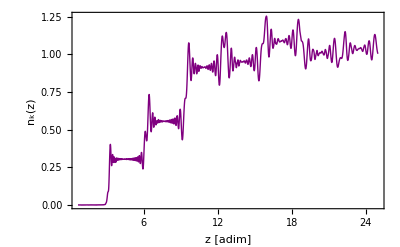

```mathematica
plotχ5 = Plot[Abs[χsol[5,z]]^2,{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{Red,Thick}]
plotnχ5 =Plot[numberχ[5,z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["n_k(z)","Times"]}],15,"Times"]},PlotStyle->{Purple,Thick}]
(*
Export[FileNameJoin[{folder,"plot_chi_k5_preheating.pdf"}],plotχ5];
Export[FileNameJoin[{folder,"plot_nchi_k5_preheating.pdf"}],plotnχ5];
*)
```

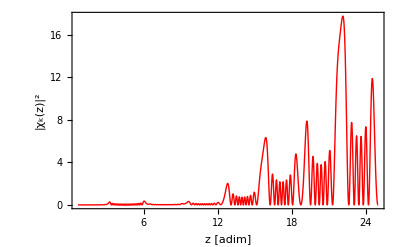

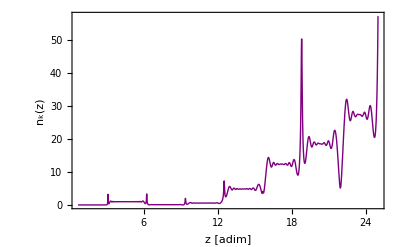

```mathematica
plotχ05 = Plot[Abs[χsol[0.5,z]]^2,{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{Red,Thick}]
plotnχ05 = Plot[numberχ[0.5,z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z [adim]","Times"]}],15,"Times"],Style[Row[{Style["n_k(z)","Times"]}],15,"Times"]},PlotStyle->{Purple,Thick}]
(*
Export[FileNameJoin[{folder,"plot_chi_k05_preheating.pdf"}],plotχ05];
Export[FileNameJoin[{folder,"plot_nchi_k05_preheating.pdf"}],plotnχ05];
*)
```

## Power spectrum of the Daughter field

```mathematica
nχSpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,numberχ[k,z]},{k,kList}],Row[{"Computation nχ for k = ",currentK}]]
];
```

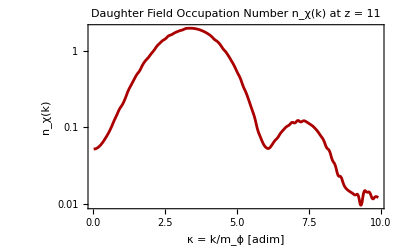

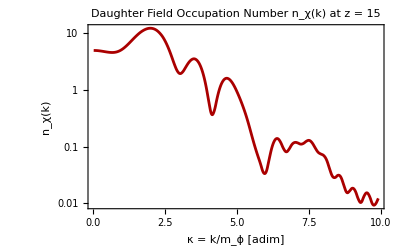

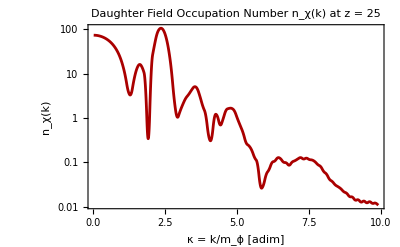

```mathematica
kValsχ=Range[0.01,10,0.1];

z1 = 7;
z2 = 15;

spectrumnχ1 = nχSpectrum[kValsχ,z1];
spectrumnχ2 = nχSpectrum[kValsχ,z2];
spectrumnχ3 = nχSpectrum[kValsχ,zMax];

plotSpectrumnχ1=ListLogPlot[spectrumnχ1,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","n_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Red]},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Occupation Number n_χ(k) at z = ``",11]]]

plotSpectrumnχ2=ListLogPlot[spectrumnχ2,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","n_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Red]},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Occupation Number n_χ(k) at z = ``",15]]]

plotSpectrumnχ3=ListLogPlot[spectrumnχ3,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","n_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Red]},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Occupation Number n_χ(k) at z = ``",zMax]]]
```

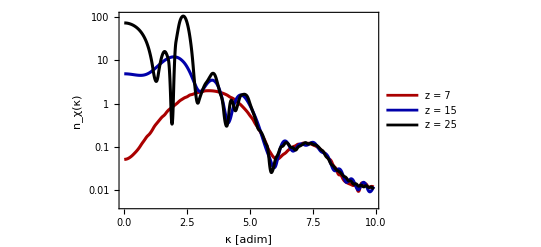

```mathematica
plotSpectranχ=ListLogPlot[{spectrumnχ1,spectrumnχ2,spectrumnχ3},Joined->True,InterpolationOrder->2,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["κ [adim]","Times"]}],15,"Times"],Style[Row[{Style["n_χ(κ)","Times"]}],15,"Times"]},PlotStyle->{{Thickness[0.0055],Darker[Red]},{Thickness[0.0055],Darker[Blue]},{Thickness[0.0055],Darker[Black]}   },PlotLegends->Placed[LineLegend[{Row[{"z = ",z1}],Row[{"z = ",z2}],Row[{"z = ",zMax}]},LegendFunction->"Frame"],{0.8,0.65}]]
(*
Export[FileNameJoin[{folder,"spectra_number_preheating.pdf"}],plotSpectranχ];
*)
```

```mathematica
(* Campo fisico *)
PSχphy[k_,z_]:=  k^3/(2 π^2)(Abs[χsol[k,z]]^2  - 1/(2Sqrt[ω2[z,k]]) );
χphySpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχphy[k,z]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];

PSχ[k_,z_]:=k^3/(2 π^2)  Abs[χsol[k,z]]^2 ;
χSpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχ[k,z]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];
```

```mathematica
(* Log plot is not well-suited for modes with zero value !!
spectrumχ1 = χSpectrum[kValsχ,z1];
spectrumχ1new = χphySpectrum[kValsχ,z1];

spectrumχ2 = χSpectrum[kValsχ,z2];
spectrumχ2new = χphySpectrum[kValsχ,z2];

spectrumχ3 = χSpectrum[kValsχ,zMax];
spectrumχ3new= χphySpectrum[kValsχ,zMax];

plotSpectrumnχ1=ListLogPlot[{spectrumχ1,spectrumχ1new},Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","χ_z(κ)"},PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Darker[Blue]}},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Power spectrum χ_z(k) at z = ``",11]]]

plotSpectrumnχ2=ListLogPlot[{spectrumχ2,spectrumχ2new},Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","χ_z(κ)"},PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Darker[Blue]}},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Power spectrum χ_z(k) at z = ``",15]]]

plotSpectrumnχ3=ListLogPlot[{spectrumχ3,spectrumχ3new},Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","χ_z(κ)"},PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Darker[Blue]}},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Power spectrum χ_z(k) at z = ``",zMax]]]
*)
```

# GW

## Compute the un-equal time Power spectrum of GWs

```mathematica
kMinGrid=0.01;
kMaxGrid=2*q^(1/4);
dk=0.1;

(* Griglia *)
nzpoints=100; 
dz=(zMax-zIn)/nzpoints;
zVals=Range[zIn,zMax,dz];

χphys[k_,z_]:=χsol[k,z]-χvac[k,z];
gridData=Flatten[Table[Table[{{kV,zV},χphys[kV,zV]},{zV,zVals}],{kV,kMinGrid,kMaxGrid,dk}],1];
χgrid=Interpolation[gridData,InterpolationOrder->3];
```

```mathematica
(* Funzioni *)
qVec[k_,p_,x_]:=Sqrt[k^2+p^2-2*k*p*x];

kCutoff = Round[qeff[zIn-bpar]^(1/4)]+1;
selectχgrid[k_,z_]:=If[k<=kMinGrid||k>=kCutoff,0.0,χgrid[k,z]];

AbsIAdimSquared[xq0_?NumericQ,xq_?NumericQ,xp_?NumericQ,x_?NumericQ]:=Block[{xqp,chiValsP,chiValsQp,productField,fourierPhase,dotProduct},
xqp=qVec[xq,xp,x];

If[xp>=kCutoff||xqp>=kCutoff,Return[0.0]];

Quiet[
chiValsP=Map[selectχgrid[xp,#]&,zVals];
chiValsQp=Map[selectχgrid[xqp,#]&,zVals];
];

productField=chiValsP*chiValsQp;
fourierPhase=Exp[I*xq0*zVals];

dotProduct=fourierPhase.productField*dz;

Abs[dotProduct]^2
];

PΠAdim[xq0_?NumericQ,xq_?NumericQ,xpSteps_Integer:50,xSteps_Integer:20]:=Block[{xpMax,dxp,dx,xpGrid,xGrid,sumVal},
xpMax=kCutoff;
dxp=(xpMax-0.1)/xpSteps;
dx=2.0/xSteps;

xpGrid=Range[0.1,xpMax,dxp];
xGrid=Range[-1.0,1.0,dx];

Quiet[
sumVal=ParallelSum[xp^6(1-x^2)^2  AbsIAdimSquared[xq0,xq,xp,x],{xp,xpGrid},{x,xGrid}];
];

1/(4 π^2) sumVal*dxp*dx
];

Δhadim[xq0_?NumericQ,xq_?NumericQ,zvalue_?NumericQ]:=Block[{pAdimVal},
pAdimVal=PΠAdim[xq0,xq];
2/π^2 xq^3/((xq0^2 - xq^2)^2)pAdimVal
];
```

```mathematica
(* GW off-shell *)
xqPoints=Range[0.1,25,4];

Δhq03q=Table[{xqVal,Δhadim[3*xqVal,xqVal,zMax]},{xqVal,xqPoints}];
Δhq05q=Table[{xqVal,Δhadim[5*xqVal,xqVal,zMax]},{xqVal,xqPoints}];
Δhq010q=Table[{xqVal,Δhadim[10*xqVal,xqVal,zMax]},{xqVal,xqPoints}];

(* Save data 
Export[FileNameJoin[{folder,"GW preheating 3.wdx"}],Δhq03q];
Export[FileNameJoin[{folder,"GW preheating 5.wdx"}],Δhq05q];
Export[FileNameJoin[{folder,"GW preheating 10.wdx"}],Δhq010q];
*)
(*
(* Import data *)
Δhq03q = Import[FileNameJoin[{folder,"GW preheating 3.wdx"}]];
Δhq05q = Import[FileNameJoin[{folder,"GW preheating 5.wdx"}]];
Δhq010q = Import[FileNameJoin[{folder,"GW preheating 10.wdx"}]];
*)
```

ListLogLogPlot::ioproc: {{-2.30259,2.29868},{1.41099,-3.3514},{2.09186,-4.787},{2.49321,-5.79061},{2.77882,-7.84185},{3.00072,-8.75622},{3.18221,Indeterminate}} may contain non-machine-precision numbers, complex numbers or invalid entries.

ListLogLogPlot::ioproc: {{-2.30259,0.112572},{1.41099,-5.957},{2.09186,-6.41316},{2.49321,-8.3647},{2.77882,-9.09766},{3.00072,-11.4866},{3.18221,Indeterminate}} may contain non-machine-precision numbers, complex numbers or invalid entries.

ListLogLogPlot::ioproc: {{-2.30259,-2.83731},{1.41099,-8.26727},{2.09186,-9.31059},{2.49321,-11.0208},{2.77882,-12.6496},{3.00072,-13.0773},{3.18221,Indeterminate}} may contain non-machine-precision numbers, complex numbers or invalid entries.

General::stop: Further output of ListLogLogPlot::ioproc will be suppressed during this calculation.

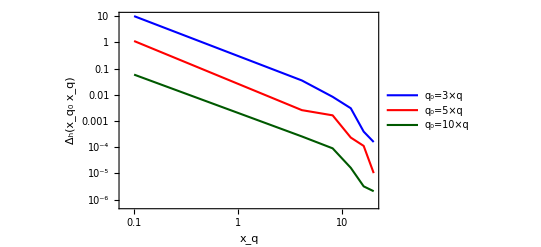

```mathematica
plotGWoffshellPreheating = loglogPlot=ListLogLogPlot[{Δhq03q,Δhq05q,Δhq010q},Joined->True,InterpolationOrder->3,Frame->True,AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{SubscriptBox["x","q"]}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["Δ","h"],"(",SubscriptBox["x",SubscriptBox["q","0"]],SubscriptBox["x","q"],")"}],TraditionalForm]],FontSize->13]},PlotStyle->{{Blue,AbsoluteThickness[1.5]},{Red,AbsoluteThickness[1.5]},{DarkGreen,AbsoluteThickness[1.5]}},
PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","3×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","5×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","10×q"}],TraditionalForm]],FontSize->13]},LegendFunction->"Frame"],{0.22,0.25}]]
(*
Export[FileNameJoin[{folder,"GW_offshell_Preheating.pdf"}],plotGWoffshellPreheating];
*)
```

## Fit decay law

```mathematica
exponentialFit=NonlinearModelFit[Δhq03q[[;;6]],A*Exp[b*x],{A,b},x]
exponentialFit["BestFit"]
```

FittedModel[…]

222.876 ⅇ^(-2.18764 x)

-0.07762-2.35463 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.07762 | 0.434147 | -0.178787 | 0.866795
x | -2.35463 | 0.180762 | -13.0262 | 0.000200453

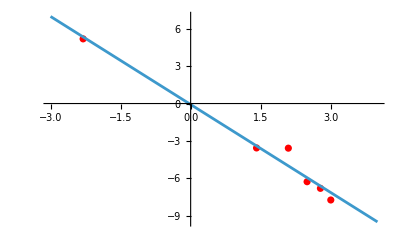

```mathematica
(* define the log data *)
logData3=Log[Δhq03q[[;;6]]];

(* Fit : param1 + param2*Log[x]*)
logFit3=LinearModelFit[logData3,x,x];
logFit3["BestFit"]
logFit3["ParameterTable"]

Show[ListPlot[logData3,PlotStyle->Red],Plot[logFit3[x],{x,-3,4}],PlotRange->All]
```

-2.67296-2.32115 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.67296 | 0.658635 | -4.05833 | 0.0153698
x | -2.32115 | 0.27423 | -8.46425 | 0.00106765

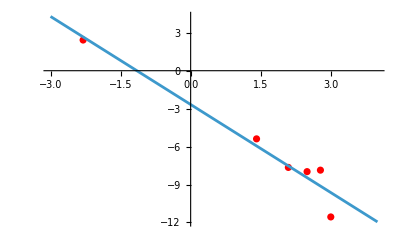

```mathematica
(* define the log data *)
logData5=Log[Δhq05q[[;;6]]];

(* Fit : param1 + param2*Log[x]*)
logFit5=LinearModelFit[logData5,x,x];
logFit5["BestFit"]
logFit5["ParameterTable"]

Show[ListPlot[logData5,PlotStyle->Red],Plot[logFit5[x],{x,-3,4}],PlotRange->All]
```

-5.99176-2.11665 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.99176 | 0.982951 | -6.09569 | 0.00366352
x | -2.11665 | 0.409262 | -5.17188 | 0.00664338

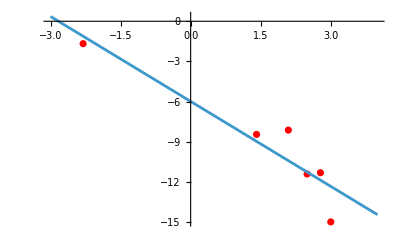

```mathematica
(* define the log data *)
logData10=Log[Δhq010q[[;;6]]];

(* Fit : param1 + param2*Log[x]*)
logFit10=LinearModelFit[logData10,x,x];
logFit10["BestFit"]
logFit10["ParameterTable"]

Show[ListPlot[logData10,PlotStyle->Red],Plot[logFit10[x],{x,-3,4}],PlotRange->All]
```

```mathematica
(*
OnShellIntegral[xq_?NumericQ, xp_?NumericQ, x_?NumericQ, zvalue_?NumericQ] := Block[{xkp, Jcos, Jsin, fieldProduct},
   xkp = qVec[xq,xp, x];
   If[xkp < kMinGrid, xkp = kMinGrid];
   If[xkp > kMaxGrid, xkp = kMaxGrid];
   
   Quiet[
    Jcos = NIntegrate[Cos[xq*z] * Re[χgrid[xp, z]] * Re[χgrid[xkp, z]],{z, zIn, zvalue},Method -> "LocalAdaptive",MaxRecursion -> 8, AccuracyGoal -> 4];
    Jsin = NIntegrate[Sin[xq*z] *Re[χgrid[xp, z]] * Re[χgrid[xkp, z]],{z, zIn, zvalue},Method -> "LocalAdaptive", MaxRecursion -> 8,AccuracyGoal -> 4];
   ];
   
   Jcos^2 + Jsin^2
];

dρdlogq[xq_?NumericQ, zvalue_?NumericQ, pSteps_Integer : 20, xSteps_Integer : 10] := Block[{xpMax, dxp, dx, xpGrid, xGrid, sumVal},
   xpMax = 20.0; 
   dxp = (xpMax - 0.1)/pSteps;
   dx = 2.0/xSteps;
   
   xpGrid = Range[0.1, xpMax, dxp];
   xGrid = Range[-1.0, 1.0, dx];
   
   sumVal = ParallelSum[Block[{timeIntVal},
         timeIntVal = OnShellIntegral[xq, xpVal, xVal, zvalue];xpVal^6 * (1 - xVal^2)^2 * timeIntVal * dxp * dx],{xpVal, xpGrid}, {xVal, xGrid}];

  xq^3/(2 π^2)sumVal
];
*)
```

```mathematica
(* 
kGWList = Range[1.0, 15.0, 2.0];
zEvaluation = 15.0; 

gwEnergyData = Table[{kVal, dρdlogq[kVal, zEvaluation]},{kVal, kGWList}];

(* Generazione del plot accademico dello spettro fisico *)
plotGWEnergy = ListLinePlot[
   gwEnergyData, 
   Joined -> True, 
   InterpolationOrder -> 3,
   Frame -> True,
   FrameLabel -> {
     Style["Dimensionless wave number κ = k/m_ϕ", Bold, 11], 
     Style["d\!\(\*SubscriptBox[\(ρ\), \(GW\)]\)/d ln(κ) [unita' adim.]", Bold, 11]
   },
   PlotStyle -> {Thickness[0.006], RGBColor[0.1, 0.6, 0.25]}, (* Verde brillante classico da pubblicazione *)
   GridLines -> Automatic,
   PlotLabel -> Style["On-Shell Gravitational Wave Energy Density Spectrum", Bold, 12]
];

Print[plotGWEnergy];
*)
```